# 2. Labor

## 1.feladat

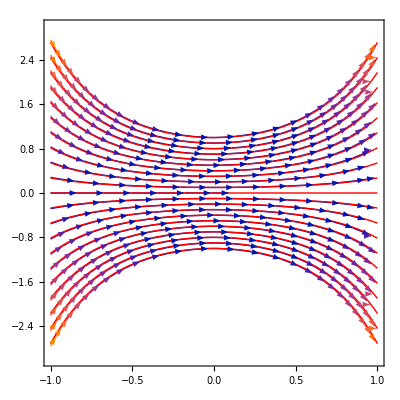

```mathematica
ySol=Table[DSolveValue[{y'[x]==2x*y[x],y[0]==(i-1)/10-1},y,x],{i,1,21,1}];
Show[
Table[
StreamPlot[{1,2*x*y},{x,-1,1},{y,-3,3},StreamPoints->{{0,i}}],{i,-1,1,0.1}],
Table[Plot[ySol[[i]][x],{x,-1,1},PlotStyle->{Thin,Red}],
 {i,1,21}]
]
```

## 2.feladat

```mathematica
x0=0;
xmax=1;
y0=1;

f=Function[{x,y},2*x*y];
eulermodszer[n_,x0_,xmax_,y0_,f_]:=
(h=(xmax-x0)/n;
u={0};
v={y0};
For[ i = 2,i<=n+1,++i,{
AppendTo[u,u[[i-1]]+h],
AppendTo[v,v[[i-1]]+h*f[u[[i-1]],v[[i-1]]]]
}
];
Table[{u[[i]],v[[i]]},{i,1,n}]
);

soly=DSolveValue[{y'[x]==2*y[x]*x,y[0]==y0},y,x]

Manipulate[
Show[
Plot[soly[x],{x,0,1},PlotStyle->Blue],
ListLinePlot[eulermodszer[m,0,1,1,f],ColorFunction->Function[{x,y},Red]]
],{m,2,25,1}]
```

Function[{x},ⅇ^(x^2)]

InterpolatingFunction[…]

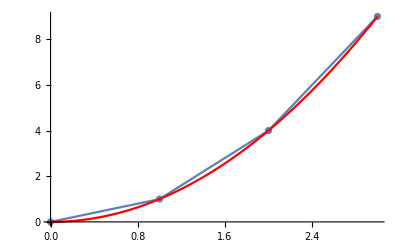

```mathematica
l=Table[{i,i^2},{i,0,3}];
il=Interpolation[l]

Show[ListPlot[l],ListLinePlot[l],Plot[il[x],{x,0,3},PlotStyle->Red]]
```

## 3.feladat

Function[{x},ⅇ^(x^2)]

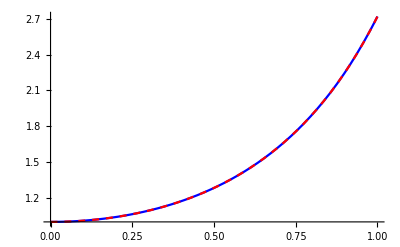

```mathematica
n=10;
x0=0;
xmax=1;
y0=1;
f=Function[{x,y},2*x*y];

rungekuttamodszer[n_,x0_,xmax_,y0_,f_]:=(
h=(xmax-x0)/n;
u={0};
v={1};
For[i=2,i<=n+1,++i,{
k1=f[u[[i-1]],v[[i-1]]],
k2=f[u[[i-1]]+h/2,v[[i-1]]+h/2*k1],
k3=f[u[[i-1]]+h/2,v[[i-1]]+h/2*k2],
k4=f[u[[i-1]]+h,v[[i-1]]+h*k3],
AppendTo[u,u[[i-1]]+h],
AppendTo[v,v[[i-1]]+h/6*(k1+2*k2+2*k3+k4)]
}];
Table[{u[[i]],v[[i]]},{i,1,n+1}]
);

interp=Interpolation[rungekuttamodszer[n,x0,xmax,y0,f]];

szimb=DSolveValue[{y'[x]==2*y[x]*x,y[0]==1},y,x]

Show[
Plot[interp[x],{x,0,1},PlotStyle->Blue],
Plot[szimb[x],{x,0,1},PlotStyle->{Red,Dashed}]
]
```

## 4.feladat

Function[{x},12+25 ⅇ^(r x)]

{-0.328504}

{Function[{x},12+25 ⅇ^(-0.328504 x)]}

{12+25 ⅇ^(-0.328504 t)}

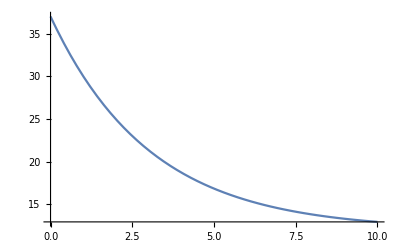

```mathematica
(*   
37C krumpli & 12C pince
1 ora mulva: 30C

elso 10 ora abrazolas
*)

soly=DSolveValue[{y'[x]==r*(y[x]-12),y[0]==37},y,x]
r0=r/.NSolve[soly[1]==30,r,Reals]
soly/. NSolve[soly[1]==30,r,Reals]
lehulesfuggveny=12+25*Exp[r0*t]
Plot[lehulesfuggveny,{t,0,10}]
```

## 5. feladat

Function[{t},3 (4+5 ⅇ^(k t))]

{-0.405465}

{-1.25985}

{10 44}

{3 (4+5 ⅇ^(-0.405465 t))}

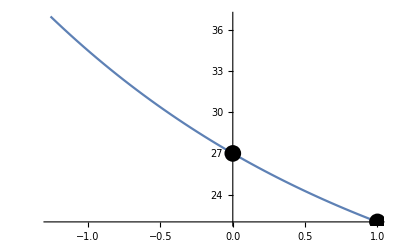

```mathematica
(* 12C pince homerseklet
27C holttest
1ora mulva holttest 22

halal bealta 37
halal idopont?
*)
soly=DSolveValue[{y'[t]==k*(y[t]-12),y[0]==27},y,t]

(* 1 oraval halal utan 22*)
k0=k/.NSolve[soly[1]==22,k,Reals]

(* t0 meghalas idopont*)
t0=t/.NSolve[3*(4+5*Exp[k0*t])==37,t,Reals]
h=UnitConvert[Quantity[12+t0,"Hours"],MixedUnit[{"Hours","Minutes","Seconds"}]]

hulesfuggv=3*(4+5*Exp[k0*t])

Show[(*   *)
{Plot[hulesfuggv,{t,t0[[1]],1}]},{Graphics[{PointSize[0.03],Point[{0,27}]}]},{Graphics[{PointSize[0.03],Point[{1,22}]}]}]
```